```mathematica
initialSeedPoly[exp_,x_]:=Expand[exp/.{x->(x-Coefficient[exp,x^(Exponent[exp,x]-1)]/Exponent[exp,x])}];
stageTwoSeedPoly[exp_,x_]:=Expand[x^Exponent[exp,x]+Sum[-Abs[Coefficient[exp,x^i]]x^i,{i,1,Exponent[exp,x]-2}]-Abs[exp-Sum[Coefficient[exp,x^i]x^i,{i,1,Exponent[exp,x]}]]];
initialSeed[exp_,x_]:=
Block[
{n,exp1,i,c1},
i=0;
n =Exponent[exp,x];
c1=Coefficient[exp,x^(n-1)];
exp1=stageTwoSeedPoly[initialSeedPoly[exp,x],x];
While[
Not[And[(exp1/.x->i)≤0,(exp1/.x->i+1)≥0]],
i=i+1;
];
Return[Table[-c1/n+Round[i+1]Exp[I*(2Pi/n*(k-1)+Pi/2/n)],{k,1,n}]];
];
PACARootFinder[exp_,x_]:=If[
Exponent[exp,x]==1,
-(exp-x Coefficient[exp,x])/Coefficient[exp,x],
Block[
{n1,z,z1,i,flag},
n1=Exponent[exp,x];
z =N[initialSeed[exp,x]];
While[True,
z1 = Table[z[[i]]+(exp/.x->z[[i]])/((exp/.x->z[[i]])*Sum[If[k≠i,1/(z[[i]]-z[[k]]),0],{k,1,n1}]-(D[exp,x]/.x->z[[i]])),{i,1,n1}];
flag=True;
For[i=1,i≤n1,i++,flag=And[flag,Abs[z[[i]]-z1[[i]]]<0.01]];
If[flag,Break[]];
For[i=1,i≤n1,i++,z[[i]]=z1[[i]]];
];
Return[Round[z1,0.000001]];
]];
NewPACARootFinder[exp_,x_]:=
Block[
{n,cp,exp1,exp2,exp3,c0},
n=Exponent[exp,x];
cp=Coefficient[exp,x^n];
exp1=N[Expand[exp/cp]];
c0=exp1/.x->0;
(*Refining the coefficients*)
exp2=If[Abs[c0]<0.01,Sign[Re[c0]]0.01+I Sign[Im[c0]]0.01,Round[c0,0.01]]+Sum[ If[Abs[Coefficient[exp1,x^i]]<0.01,Sign[Re[Coefficient[exp1,x^i]]]0.01+I Sign[Im[Coefficient[exp1,x^i]]]0.01,Round[Coefficient[exp1,x^i] ,0.01]]*x^i,{i,1,n}];
cp=Coefficient[exp2,x^n];
exp3=N[Expand[exp2/cp]];
Return[PACARootFinder[exp3,x]]
];
```

```mathematica
Clear[runPython];
runPython::badCommand="Python code failed to run with message `StandardError`";
$pyimports="from random import randint";
runPython[str_String,imports_:$pyimports]:=Module[{pyscrpt=ToString[$pyimports<>str,CharacterEncoding->"ASCII"],file=CreateTemporary[],res},Export[file,pyscrpt,"Text"];
res=RunProcess[{"python",file}];
DeleteFile[file];
If[res["ExitCode"]≠0,Return@Failure["badCommand",<|"MessageTemplate":>runPython::badCommand,"MessageParameters"-><|"Message"->res["StandardError"]|>|>],Return@ImportString@res["StandardOutput"]]];
```

```mathematica
runPython[StringJoin["
import os
os.system('ps -p ",ToString[$ProcessID]," -v')
os.system('ps M ",ToString[$ProcessID]," | wc -l')"
]]
```

PID STAT      TIME  SL  RE PAGEIN      VSZ    RSS   LIM     TSIZ  %CPU %MEM COMMAND
 5675 R      0:02.88   0   0      0  2756028  92436     -        0   0.4  1.1 /Applications/Mathematica.app/Contents/MacOS/WolframKernel -wstp -mathlink -linkprotocol SharedMemory -linkconnect -linkname tsdux_shm
      20

```mathematica
Block[
{n,exp,str,x},
n=9;
exp=Sum[(1+RandomReal[])x^i,{i,0,n}];
NewPACARootFinder[exp,x];
str=runPython[StringJoin["
import os
os.system('ps -p ",ToString[$ProcessID]," -v')
os.system('ps M ",ToString[$ProcessID]," | wc -l')"
]];
Print[str];
NSolve[exp==0,x];
str=runPython[StringJoin["
import os
os.system('ps -p ",ToString[$ProcessID]," -v')
os.system('ps M ",ToString[$ProcessID]," | wc -l')"
]];
Print[str];
]
```

PID STAT      TIME  SL  RE PAGEIN      VSZ    RSS   LIM     TSIZ  %CPU %MEM COMMAND
 5675 R      0:19.70   0   0      0  2757884  95156     -        0   0.4  1.1 /Applications/Mathematica.app/Contents/MacOS/WolframKernel -wstp -mathlink -linkprotocol SharedMemory -linkconnect -linkname tsdux_shm
      20

PID STAT      TIME  SL  RE PAGEIN      VSZ    RSS   LIM     TSIZ  %CPU %MEM COMMAND
 5675 R      0:19.82   0   0      0  2757884  95156     -        0  33.1  1.1 /Applications/Mathematica.app/Contents/MacOS/WolframKernel -wstp -mathlink -linkprotocol SharedMemory -linkconnect -linkname tsdux_shm
      20

```mathematica
Mean[{6.9,0.4,0.4,15.1,16.2,3.7,13.0,11.7,10.7,0.4,0.4,12.4,2.7,0.4,0.9,0.4}]
Length[{6.9,0.4,0.4,15.1,16.2,3.7,13.0,11.7,10.7,0.4,0.4,12.4,2.7,0.4,0.9,0.4}]
```

5.98125

16

```mathematica
Mean[{40.3,32.9,36.0,44.7,47.0,38.8,44.1,45.5,44.7,48.8,30.3,45.5,38.0,36.4,38.5,33.1}]
Length[{40.3,32.9,36.0,44.7,47.0,38.8,44.1,45.5,44.7,48.8,30.3,45.5,38.0,36.4,38.5,33.1}]
```

40.2875

16

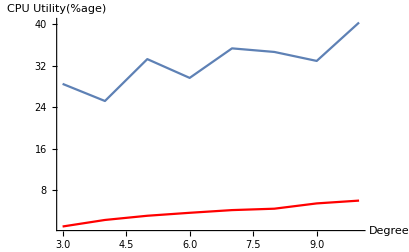

```mathematica
Show[
ListLinePlot[{{3,0.99},{4,2.25},{5,3.06},{6,3.63},{7,4.15},{8,4.42},{9,5.44},{10,5.98}},PlotStyle->Red],
ListLinePlot[{{3,28.47},{4,25.17},{5,33.24},{6,29.62},{7,35.31},{8,34.62},{9,32.89},{10,40.29}}],PlotRange->All,
AxesOrigin->{2,0},AxesLabel->{"Degree","CPU Utility(%age)"}
]
```

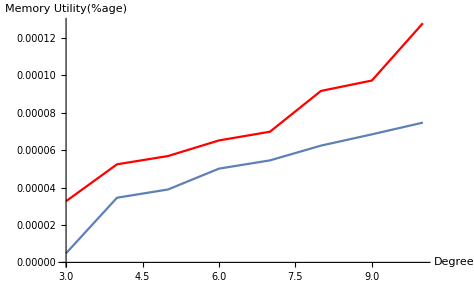

```mathematica
Block[
{n,exp,memstart,memend,totalmem,MemRootFind,MemRootFind2,x},
MemRootFind=Table[{i,0},{i,3,10}];
MemRootFind2=Table[{i,0},{i,3,10}];
totalmem=MemoryAvailable[];
For[
n=3,n≤10,n++,
exp=Sum[(1+RandomReal[])x^i,{i,0,n}];
memstart=MemoryInUse[];
NewPACARootFinder[exp,x];
memend=MemoryInUse[];
MemRootFind[[n-2]][[2]]=Abs[memstart-memend]/totalmem*100;
memstart=MemoryInUse[];
NSolve[exp==0,x];
memend=MemoryInUse[];
MemRootFind2[[n-2]][[2]]=Abs[memstart-memend]/totalmem*100;
];
Show[
ListLinePlot[MemRootFind,PlotStyle->Red],
ListLinePlot[MemRootFind2],AxesOrigin->{3,0},AxesLabel->{"Degree","Memory Utility(%age)"}
]
]
```

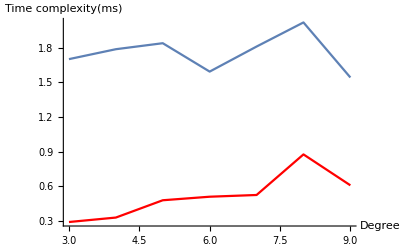

```mathematica
Block[
{n,exp,memstart,memend,totalmem,MemRootFind,MemRootFind2,x},
MemRootFind=Table[{i,0},{i,3,9}];
MemRootFind2=Table[{i,0},{i,3,9}];
For[
n=3,n≤9,n++,
exp=Sum[x^i,{i,0,n}];
memstart=AbsoluteTime[];
NewPACARootFinder[exp,x];
memend=AbsoluteTime[];
MemRootFind[[n-2]][[2]]=Abs[memstart-memend]*10^3/n;
memstart=AbsoluteTime[];
NSolve[exp==0,x];
memend=AbsoluteTime[];
MemRootFind2[[n-2]][[2]]=Abs[memstart-memend]*10^3;
];
Show[
ListLinePlot[MemRootFind,PlotStyle->Red],
ListLinePlot[MemRootFind2],AxesOrigin->{3,0},AxesLabel->{"Degree","Time complexity(ms)"},PlotRange->All
]
]
```